## Deep Learning with MLP

```mathematica
Clear["Global`*"];
<<CIP`MLP`
<<CIP`Graphics`
<<CIP`CalculatedData`
<<CIP`DataTransformation`
```

### Data around Sum of Bumps

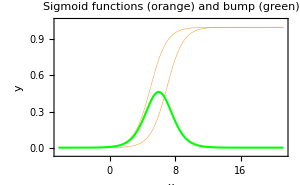

```mathematica
interval={5.,7.};
pureSigmoid1=Function[x,CIP`MLP`SigmoidFunction[x-interval[[1]]]];
pureSigmoid2=Function[x,CIP`MLP`SigmoidFunction[x-interval[[2]]]];
pureBump=Function[x,CIP`MLP`BumpFunction[x,interval]];
pureFunctions={pureSigmoid1,pureSigmoid2,pureBump};
argumentRange={-5.0,20.0};
plotRange={0.0,1.0};
plotStyle={{Thickness[0.001],Orange},{Thickness[0.001],Orange},{Thickness[0.005],Green}};
labels={"x","y","Sigmoid functions (orange) and bump (green)"};
CIP`Graphics`Plot2dFunctions[pureFunctions,argumentRange,plotRange,plotStyle,labels]
```

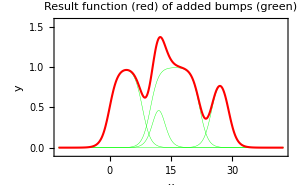

```mathematica
interval1={0.,8.};
pureBump1=Function[x,CIP`MLP`BumpFunction[x,interval1]];
interval2={11.,13.};
pureBump2=Function[x,CIP`MLP`BumpFunction[x,interval2]];
interval3={10.,22.};
pureBump3=Function[x,CIP`MLP`BumpFunction[x,interval3]];
interval4={25.,29.};
pureBump4=Function[x,CIP`MLP`BumpFunction[x,interval4]];
pureBumpSum=Function[x,CIP`MLP`BumpFunction[x,interval1]+CIP`MLP`BumpFunction[x,interval2]+CIP`MLP`BumpFunction[x,interval3]+CIP`MLP`BumpFunction[x,interval4]];
pureFunctions={pureBump1,pureBump2,pureBump3,pureBump4,pureBumpSum};
argumentRange={-10,40};
plotRange={0.0,1.5};
plotStyle={{Thickness[0.001],Green},{Thickness[0.001],Green},{Thickness[0.001],Green},{Thickness[0.001],Green},{Thickness[0.005],Red}};
labels={"x","y","Result function (red) of added bumps (green)"};
CIP`Graphics`Plot2dFunctions[pureFunctions,argumentRange,plotRange,plotStyle,labels]
```

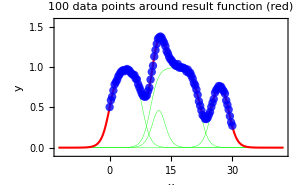

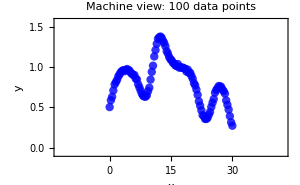

Standard Deviation = 0.01

```mathematica
numberOfData=100;
standardDeviation=0.01;
standardDeviationRange={standardDeviation,standardDeviation};
simulatedDataArgumentRange={0.0,30.0};
xyErrorData=CIP`CalculatedData`GetXyErrorData[pureBumpSum,simulatedDataArgumentRange,numberOfData,standardDeviationRange];
dataSet=CIP`DataTransformation`TransformXyErrorDataToDataSet[xyErrorData];
labels={"x","y",StringJoin[ToString[numberOfData]," data points around result function (red)"]};
pointSize=0.02;
CIP`Graphics`PlotXyErrorDataAboveFunctions[xyErrorData,pureFunctions,argumentRange,plotRange,plotStyle,labels,GraphicsOptionPointSize->pointSize]
labels={"x","y",StringJoin["Machine view: ",ToString[numberOfData]," data points"]};
CIP`Graphics`PlotXyErrorData[xyErrorData,labels,GraphicsOptionPointSize->pointSize,GraphicsOptionArgumentRange2D-> argumentRange,GraphicsOptionFunctionValueRange2D->plotRange ]
Print[StringJoin["Standard Deviation = ",ToString[standardDeviation]]];
```

### Shallow and Deep Learning

----------------------------------------------------------------------------

MLP:

Hidden Neuron Layers   = {9}

Activation and Scaling = {{Tanh, Sigmoid}, {{-0.9, 0.9}, {0.1, 0.9}}}

----------------------------------------------------------------------------

Learning (Minimization) Steps = 1000

Root mean squared error (RMSE) = 1.578×10^-2

Calculation period [s] = 2.0314089

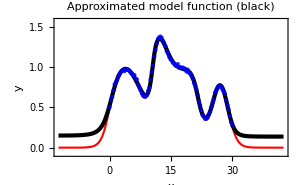

Learning (Minimization) Steps = 100000

Root mean squared error (RMSE) = 1.003×10^-2

Calculation period [s] = 6.1254823 (factor 3 slower)

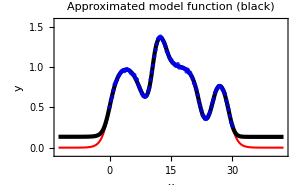

----------------------------------------------------------------------------

MLP:

Hidden Neuron Layers   = {5, 4}

Activation and Scaling = {{Tanh, Tanh, Sigmoid}, {{-0.9, 0.9}, {0.1, 0.9}}}

----------------------------------------------------------------------------

Learning (Minimization) Steps = 1000

Root mean squared error (RMSE) = 9.634×10^-3

Calculation period [s] = 3.8909310

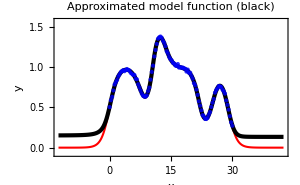

Learning (Minimization) Steps = 100000

Root mean squared error (RMSE) = 9.537×10^-3

Calculation period [s] = 4.6253629 (factor 1 slower)

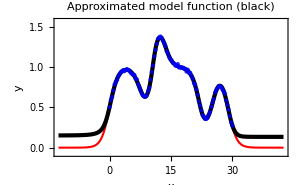

----------------------------------------------------------------------------

MLP:

Hidden Neuron Layers   = {3, 3, 3}

Activation and Scaling = {{Tanh, Tanh, Tanh, Sigmoid}, {{-0.9, 0.9}, {0.1, 0.9}}}

----------------------------------------------------------------------------

Learning (Minimization) Steps = 1000

Root mean squared error (RMSE) = 1.843×10^-2

Calculation period [s] = 5.0472715

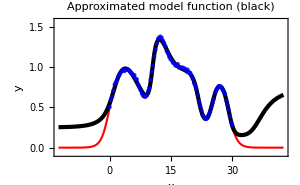

Learning (Minimization) Steps = 100000

Root mean squared error (RMSE) = 1.012×10^-2

Calculation period [s] = 15.3918338 (factor 3 slower)

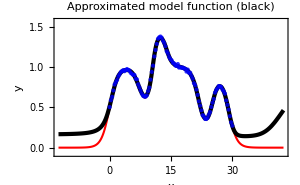

----------------------------------------------------------------------------

MLP:

Hidden Neuron Layers   = {3, 2, 2, 2}

Activation and Scaling = {{Tanh, Tanh, Tanh, Tanh, Sigmoid}, {{-0.9, 0.9}, {0.1, 0.9}}}

----------------------------------------------------------------------------

Learning (Minimization) Steps = 1000

Root mean squared error (RMSE) = 6.935×10^-2

Calculation period [s] = 5.1879085

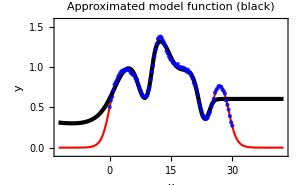

Learning (Minimization) Steps = 100000

Root mean squared error (RMSE) = 1.05×10^-2

Calculation period [s] = 68.5053869 (factor 13 slower)

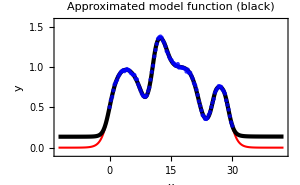

```mathematica
hyperparametersList={};

numberOfHiddenNeurons={9};
activationAndScaling={{"Tanh","Sigmoid"},{{-0.9,0.9},{0.1,0.9}}};
hyperparameters={numberOfHiddenNeurons,activationAndScaling};
AppendTo[hyperparametersList,hyperparameters];

numberOfHiddenNeurons={5,4};
activationAndScaling={{"Tanh","Tanh","Sigmoid"},{{-0.9,0.9},{0.1,0.9}}};
hyperparameters={numberOfHiddenNeurons,activationAndScaling};
AppendTo[hyperparametersList,hyperparameters];

numberOfHiddenNeurons={3,3,3};
activationAndScaling={{"Tanh","Tanh","Tanh","Sigmoid"},{{-0.9,0.9},{0.1,0.9}}};
hyperparameters={numberOfHiddenNeurons,activationAndScaling};
AppendTo[hyperparametersList,hyperparameters];

numberOfHiddenNeurons={3,2,2,2};
activationAndScaling={{"Tanh","Tanh","Tanh","Tanh","Sigmoid"},{{-0.9,0.9},{0.1,0.9}}};
hyperparameters={numberOfHiddenNeurons,activationAndScaling};
AppendTo[hyperparametersList,hyperparameters];

plotStyle={{Thickness[0.005],Red},{Thickness[0.01],Black}};
labels={"x","y","Approximated model function (black)"};
pointSize=0.01;

Do[
hyperparameters=hyperparametersList[[i]];
numberOfHiddenNeurons=hyperparameters[[1]];
activationAndScaling=hyperparameters[[2]];
Print["----------------------------------------------------------------------------"];
Print["MLP:"];
Print[StringJoin["Hidden Neuron Layers   = ",ToString[numberOfHiddenNeurons]]];
Print[StringJoin["Activation and Scaling = ",ToString[activationAndScaling]]];
Print["----------------------------------------------------------------------------"];
maximumIterations=1000;
Print[StringJoin["Learning (Minimization) Steps = ",ToString[maximumIterations]]];
start=AbsoluteTime[];
mlpInfo=
CIP`MLP`FitMlp[
dataSet,
numberOfHiddenNeurons,
MlpOptionMaximumIterations->maximumIterations,
MlpOptionActivationAndScaling->activationAndScaling
];
period1=AbsoluteTime[]-start;
pureMlpFunction=Function[x,CalculateMlpValue2D[x,mlpInfo]];
pureFunctions={pureBumpSum,pureMlpFunction};
CIP`MLP`ShowMlpSingleRegression[{"RMSE"},dataSet,mlpInfo];
Print[StringJoin["Calculation period [s] = ",ToString[period1]]];
Print[CIP`Graphics`PlotXyErrorDataAboveFunctions[xyErrorData,pureFunctions,argumentRange,plotRange,plotStyle,labels,GraphicsOptionPointSize->pointSize]];
maximumIterations=100000;
Print[StringJoin["Learning (Minimization) Steps = ",ToString[maximumIterations]]];
start=AbsoluteTime[];
mlpInfo=
CIP`MLP`FitMlp[
dataSet,
numberOfHiddenNeurons,
MlpOptionMaximumIterations->maximumIterations,
MlpOptionActivationAndScaling->activationAndScaling
];
period2=AbsoluteTime[]-start;
pureMlpFunction=Function[x,CalculateMlpValue2D[x,mlpInfo]];
pureFunctions={pureBumpSum,pureMlpFunction};
CIP`MLP`ShowMlpSingleRegression[{"RMSE"},dataSet,mlpInfo];
Print[StringJoin["Calculation period [s] = ",ToString[period2]," (factor ",ToString[Round[period2/period1]]," slower)"]];
Print[CIP`Graphics`PlotXyErrorDataAboveFunctions[xyErrorData,pureFunctions,argumentRange,plotRange,plotStyle,labels,GraphicsOptionPointSize->pointSize]];
Print[""],

{i,1,Length[hyperparametersList]}
]
```